## Cut avg full spectrum. 1 edge mode no mixing

```mathematica
doubleSigma[i_,m_,L_]:=1/(1+Exp[-(Mod[i+m,L,1]-L/2)])-1/(1+Exp[-(Mod[i+m,L,1]-L)])+1/(1+Exp[-(Mod[i+m,L,1]-L/2+L)])-1/(1+Exp[-(Mod[i+m,L,1]-L+L)])
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[{h0= ConstantArray[0,{L,L,2,2}];Table[h0[[i,Mod[i+2,L,1],;;,;;]]=.0*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i-2,L,1],;;,;;]]=.0*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i+1,L,1],;;,;;]]=t*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i-1,L,1],;;,;;]]=t*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i,L,1],;;,;;]]=kap*((If[i==3,.01,0]+3HeavisideTheta[-L/3-.1+Mod[i+tp,L,1]]-2)+1)*PauliMatrix[3]+m*PauliMatrix[2]+220*If[i==L/2||i==L/2+1,1,0]*PauliMatrix[3],{i,1,L}];
h0}[[1,;;,;;,;;,;;]]]
```

```mathematica
Hpos1[t_,tp_,m_,kap_,L_]:=ArrayFlatten[{h0= ConstantArray[0,{L,L,2,2}];Table[h0[[i,Mod[i+2,L,1],;;,;;]]=.0*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i-2,L,1],;;,;;]]=.0*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i+1,L,1],;;,;;]]=t*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i-1,L,1],;;,;;]]=t*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i,L,1],;;,;;]]=kap*(If[i==3,.01,0]+3HeavisideTheta[-L/3-.1+Mod[i+tp,L,1]]-2)*PauliMatrix[3]+m*PauliMatrix[2],{i,1,L}];
h0}[[1,;;,;;,;;,;;]]]
```

```mathematica
Hpos1[t_,tp_,m_,kap_,L_]:=ArrayFlatten[{h0= ConstantArray[0,{L,L,2,2}];Table[h0[[i,Mod[i+1,L,1],;;,;;]]=0*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i-1,L,1],;;,;;]]=0*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i+3,L,1],;;,;;]]=t*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i-3,L,1],;;,;;]]=t*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i,L,1],;;,;;]]=kap*PauliMatrix[3]+m*Mod[i+tp,L,1]/L*PauliMatrix[1],{i,1,L}];
h0}[[1,;;,;;,;;,;;]]]
Hpo1s[t_,tp_,m_,kap_,L_]:=ArrayFlatten[{h0= ConstantArray[0,{L,L,2,2}];Table[h0[[i,Mod[i+1,L,1],;;,;;]]=0*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i-1,L,1],;;,;;]]=0*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i+2,L,1],;;,;;]]=t*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i-2,L,1],;;,;;]]=t*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i,L,1],;;,;;]]=kap*PauliMatrix[3]+m*If[Mod[i+tp,L,1]>L/2+.1,Mod[i+tp,L,1]-L/2,Mod[i+tp,L,1]]/L*PauliMatrix[1],{i,1,L}];
h0}[[1,;;,;;,;;,;;]]]
Hpos1[t_,tp_,m_,kap_,L_]:=ArrayFlatten[{h0= ConstantArray[0,{L,L,2,2}];Table[h0[[i,Mod[i+1,L,1],;;,;;]]=t*(1+2*.1 *doubleSigma[i,tp,L]-.1)*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i-1,L,1],;;,;;]]=t*(1+2*.1 *doubleSigma[i,tp,L]-.1)*(PauliMatrix[1]-I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i+2,L,1],;;,;;]]=0.0*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}]
Table[h0[[i,Mod[i-2,L,1],;;,;;]]=0.0*(PauliMatrix[1]+I PauliMatrix[2])/2,{i,1,L}];
Table[h0[[i,Mod[i,L,1],;;,;;]]=(2*kap *doubleSigma[i,tp,L]-1kap)*PauliMatrix[3]+m*PauliMatrix[1],{i,1,L}];
(*Table[h0[[i,Mod[i,L,1],;;,;;]]=(3kap *HeavisideTheta[-L/3-.01+Mod[i+tp,L,1]]-2kap)*PauliMatrix[3]+m*PauliMatrix[2],{i,1,L}];*)
h0}[[1,;;,;;,;;,;;]]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)

Ck[t_,tp_,m_,kap_,k_]:=1/2(IdentityMatrix[2]-H[t,tp,m,kap,k]/Sqrt[-Det[H[t,tp,m,kap,k]]])
Caold[t_,tp_,m1_,kap_,L1_,ic_,fc_]:=Table[Sum[Exp[-I q1 (n-m)]*Ck[t,tp,m1,kap,q1]/L1,{q1,0,2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}],{n,ic,fc},{m,ic,fc}];
Ca[t_,tp_,m_,kap_ ,L_,ic_,fc_]:=Sum[ArrayFlatten[ReleaseHold[DiagonalMatrix[Hold /@ ConstantArray[Sum[Exp[-I k1 (-l)]*Ck[t,tp,m,kap,k1]/L,{k1,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}],fc-ic+1-IntegerPart[Abs[l]]],IntegerPart[2l]] ]] ,{l,-fc+ic,fc-ic}];
Heval[t_,tp_,m_,kap_,L1_]:= Re[Eigenvalues[ArrayFlatten[Hpos[t,tp,m,kap,L1]]]];
ESeval2[t_,tp_,m_,kap_,L1_]:= Re[Eigenvalues[ArrayFlatten[Capos[t,tp,m,kap,L1]]]];
MatrixLogSafe[x_?(MatrixQ[#1,NumericQ]&)]:=MatrixLog[x+1.*^-9 IdentityMatrix[Length[x]]]/Log[2];
berryq1[t_,tp_,m_,kap_,k_,L1_]:=(Gqq =Table[ Ck[t,tp,m,kap,kt],{kt,k}];
egqq=Table[Eigenvectors[10*IdentityMatrix[2]+Gqq[[ki,;;,;;]]],{ki,1,L1}];
egqqOrd=Table[Map[Normalize[#/#[[1]]]&,egqq[[ki,;;,;;]]],{ki,1,L1}];
egqqOrd1 =Table[egqqOrd[[ki,;;,;;]][[1]],{ki,1,L1}];
inprod=Table[Conjugate[egqqOrd1 [[q1i,;;]]].egqqOrd1 [[q1i+1,;;]],{q1i,1,L1-1}];Mod[-Im[Log[Times@@inprod[[;;]]]],2Pi]/2/Pi)
berryq2[t_,tp_,m_,kap_,k_,L1_]:=(data =Table[Ck[t,tp,m,kap,ki],{ki,k}];Mod[-Im[Log[Tr[Dot @@ data ]]],2Pi]/2/Pi)
ct[a_,b_]:=Conjugate[{a}].Transpose[{b}]
c[a_,b_]:=a.b-b.a;
ac[a_,b_]:=a.b+b.a;
berryDisorder[t_, tp_, m_, kap_, L1_]:=(C2 =IdentityMatrix[2L1]*10+ Hpos[t,tp,m,kap,L1];
posop = KroneckerProduct[DiagonalMatrix[Table[i,{i,1,L1}]],IdentityMatrix[2]];
posoppbc = MatrixExp[-I 2Pi posop /(L1)];
vec = Orthogonalize[Eigenvectors[C2]];
S = Table[Conjugate[vec[[i,;;]]].posoppbc.vec[[j,;;]],{i,L1+1,2L1},{j,L1+1,2L1}];
-Im[Log[Det[S]]]/2/Pi+1/2
)
Essum[t_, tp_, m_, kap_, L1_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0;
vecab = Orthogonalize[Eigenvectors[Cab]];
projl=Diagonal/2Matrix[Table[HeavisideTheta[L1/2+.1-i],{i,1,L1}
]];
projr=DiagonalMatrix[Table[HeavisideTheta[-L1/2-.1+i],{i,1,L1}
]];
projl2 = ArrayFlatten[{{projl-0*projr,ConstantArray[0,{L1,L1}]},{ConstantArray[0,{L1,L1}],projl-0*projr}}];
Sab=Table[Conjugate[vecab[[i,;;]]].MatrixExp[-I Pi projl2.Cab].vecab[[j,;;]],{i,L1+1,2L1},{j,L1+1,2L1}];
-Im[Log[Det[Sab.Inverse[Abs[Sab]]]]]/2/Pi
)
```

### Parameter def

```mathematica
L1=42; ic = 1; fc =L1/2;
t = 1; tp =0.;m=1.;kap=.2;
Ltp=41;
mlist=Table[tpi,{tpi,0,2,(2-0.01)/(Ltp-1)}];
clist=Table[tpi,{tpi,1,L1,(L1)/(L1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

### Main

For this example we use the following conjugate[S].profile for the potential,

```mathematica
ListAnimate[Table[ListPlot[Diagonal[Hpos[t,tp,0,kap,L1]][[1;;;;2]],PlotRange->All],{tp,1,L1}]]
```

```mathematica
Total[Diagonal[Hpos[t,1,0,kap,L1]][[;;;;2]]]
```

0.003

```mathematica
datah=Table[Transpose@{ConstantArray[mi,2L1],Re[Eigenvalues[Hpos[t,ci,mi,kap,L1]]]},{mi,mlist},{ci,clist}];
ListAnimate[Table[ListPlot[datah[[;;,i,;;,;;]],PlotStyle->Blue],{i,1,L1}] ]
```

```mathematica
datah=Table[Transpose@{ConstantArray[mi,L1],Re[Eigenvalues[Hpos[t,ci,mi,kap,L1][[1;;L1,1;;L1]]]]},{mi,mlist},{ci,clist}];
ListAnimate[Table[ListPlot[datah[[;;,i,;;,;;]],PlotStyle->Blue],{i,1,L1}] ]
```

```mathematica
dataesa=Table[Transpose@{ConstantArray[mi,L1],Re[Eigenvalues[Capos[t,ci,mi,kap,L1]]]},{mi,mlist},{ci,clist}];
ListAnimate[Table[ListPlot[dataesa[[;;,i,;;,;;]],PlotStyle->Blue],{i,1,L1}] ]
```

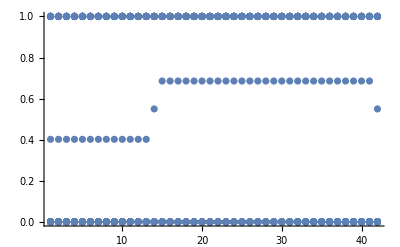

```mathematica
Show[{Table[ListPlot[dataesa[[1,;;,i,2]]],{i,1,42}]},PlotRange->{{1,42},{0,1}}]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Capos[t,ci,mi,kap,L1]]],{mi,mlist},{ci,clist}];
```

```mathematica
databerry=Table[-berryDisorder[t,0,mi,kap,L1],{mi,mlist}];
```

```mathematica
signlr3=Table[If[Total[Abs[datavec[[m,mi,i,1;;L1/2]]]^2]>.5,1/2,-1/2],{m,1,Ltp},{mi,1,L1},{i,1,L1}];
```

```mathematica
essum=.5+Sum[-dataesa[[;;,;;,i,2]]*(signlr3[[;;,;;,i]]),{i,1,L1}];
essum2=Sum[-dataesa[[;;,;;,i,2]]*(signlr3[[;;,;;,i]])*2,{i,L1/2+1,L1}];
(*essum2=Sum[dataesa[[;;,;;,i,2]]*(signlr3[[;;,;;,i]]),{i,1,L1}];*)
essum3=Table[Sum[-If[dataesa[[i,j,k,2]]>.05&&dataesa[[i,j,k,2]]<.95,dataesa[[i,j,k,2]],0]*(signlr3[[i,j,k]]-1/2),{k,1,L1}],{i,1,41},{j,1,L1}];
```

```mathematica
dataloc = Table[Chop[Re[Conjugate[datavec[[1,tpi,i,;;]]].posop.datavec[[1,tpi,i,;;]]]],{tpi,1,L1},{i,1,L1}];
```

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,L1/2+3],dataloc[[tpi,1;;L1/2+3]]},{tpi,1,L1}],PlotStyle->Blue]
```

```mathematica
ListAnimate[Table[Show[{ListPlot[Table[Chop[Re[Conjugate[datavec[[1,j,i,;;]]].posop.datavec[[1,j,i,;;]]]],{i,1,L1}],PlotRange-> {{1,40},{0,20}}],Graphics[Line[{{0,20.2},{40,20.2}}]]}],{j,1,L1}]]
```

```mathematica
ListAnimate[Table[Show[{ListPlot[Mod[essum[[;;,i]],1],PlotRange->{{1,41},{0,1}}],ListPlot[Mod[databerry,1],PlotStyle->Red]}],{i,1,L1}]]
```

```mathematica
ListAnimate[Table[Show[{ListPlot[essum2[[;;,i]],PlotRange->{{1,41},{0,1}}],ListPlot[Mod[databerry,1],PlotStyle->Red],ListPlot[Sum[essum2[[;;,j]]/L1,{j,1,L1}],PlotStyle->Black]}],{i,1,L1}]]
```

```mathematica
essum3=Table[Sum[-If[dataesa[[i,j,k,2]]>.05&&dataesa[[i,j,k,2]]<.95,dataesa[[i,j,k,2]],0]*(signlr3[[i,j,k]]-1/2),{k,1,L1}],{i,1,41},{j,1,L1}];
ListAnimate[Table[Show[{ListPlot[essum3[[;;,i]],PlotRange->{{1,41},{0,1}}],ListPlot[Mod[databerry,1],PlotStyle->Red],ListPlot[Sum[essum3[[;;,j]]/L1,{j,1,L1}],PlotStyle->Black]}],{i,1,L1}]]
```

```mathematica
Dimensions[essum3]
```

{41,42}

```mathematica
essum3[[1,1]]
```

-0.0876373